```mathematica
res=Import[FileNameJoin[{NotebookDirectory[],"out","k-likelihood-time.txt"}],"Table"];
```

```mathematica
likeli=Map[{#[[1]],#[[2]]}&,res];
```

```mathematica
time = Map[{#[[1]],#[[3]]}&,res];
```

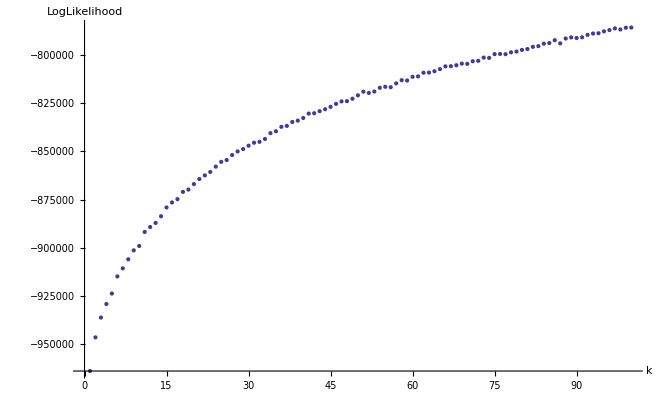

```mathematica
ListPlot[{likeli},AxesLabel->{"k","LogLikelihood"},BaseStyle->{FontWeight-> "Bold",FontSize->14}]
```

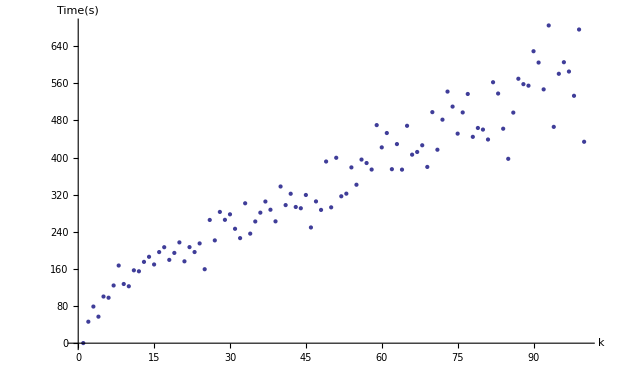

```mathematica
ListPlot[{time},AxesLabel->{"k","Time(s)"},BaseStyle->{FontWeight-> "Bold",FontSize->14}]
```